### Grammar and Growth

```mathematica
BR2[len_,rot_,ite_]:=Module[{},If[ite==1,Return[len]];
{len,{-BR2[len/1,rot,ite-1],BR2[len/1,rot,ite-1]}}]
Column[(δ1=NormalDistribution[2,.01];
δ2=NormalDistribution[6,.01];
LinkLength[len_]:=len/RandomVariate@δ1;
LinkRotation[rot_]:=π/RandomVariate@δ2;
BR2[1,π/6,#])&/@{1,2,3,4}]
```

1
{1,{-1,1}}
{1,{{-1,{1,-1}},{1,{-1,1}}}}
{1,{{-1,{{1,{-1,1}},{-1,{1,-1}}}},{1,{{-1,{1,-1}},{1,{-1,1}}}}}}

```mathematica
BR2[len_,rot_,ite_]:=Module[{},If[ite==0,Return[]];
{Line[{{0,0},{0,len}}],Translate[{Rotate[{BR2[LinkLength@len,rot,ite-1]},LinkRotation@rot,{0,0}],Rotate[{BR2[LinkLength@len,rot,ite-1]},-LinkRotation@rot,{0,0}]},{0,len}]}]
Row[(δ1=NormalDistribution[2,.01];
δ2=NormalDistribution[6,.01];
LinkLength[len_]:=len/RandomVariate@δ1;
LinkRotation[rot_]:=π/RandomVariate@δ2;
Graphics[BR2[1,π/6,#],PlotRange->{{-.9,.9},{0,2.2}},ImageSize->64])&/@{1,2,3,4,5,6}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### Stochastics & Statistics

```mathematica
n=3;
series:=RandomInteger[{1,6},n]
series
```

{5,3,1}

```mathematica
series
```

{4,4,4}

#### The Law of Large Numbers (LNN)

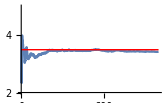
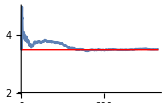
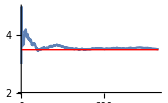

```mathematica
n=1000;
Row[Show[ListLinePlot[Accumulate@RandomInteger[{1,6},n]/Range@n,PlotRange->{{0,n},{2.,5}},ImageSize->168],Graphics[{Red,Line[{{0,3.5},{n,3.5}}]}]]&/@{1,1,1}]
```

{5,1,2,4,6,2,6,4,1,6,6,4,1,2,2,1,3,2,3,2,6,«59»,4,1,5,1,3,1,5,2,6,1,4,3,6,6,1,1,1,4,1,4}

{1→20,2→17,3→18,4→17,5→6,6→22}

{1/5,17/100,9/50,17/100,3/50,11/50}

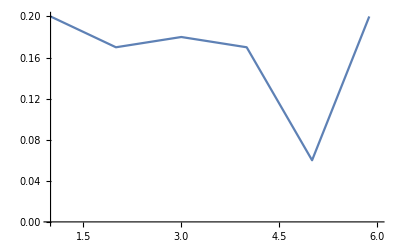

```mathematica
pln=100;
plt=RandomInteger[{1,6},pln];Short@plt
pct=SortBy[Normal@Counts@plt,First]
pctN=#[[2]]/pln&/@(List@@#&/@pct)
ListLinePlot[pctN,PlotRange->{{1,6},{0,.2}}]
```

{1,4,6,5,4,4,1,3,4,4,6,4,4,5,5,1,4,5,4,6,«99960»,3,4,1,5,1,1,2,4,1,6,2,3,5,4,1,3,2,3,1,5}

{1→16730,2→16730,3→16778,4→16638,5→16540,6→16584}

{1673/10000,1673/10000,8389/50000,8319/50000,827/5000,2073/12500}

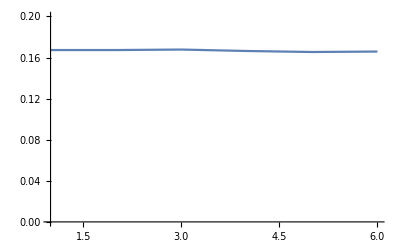

```mathematica
pln=100000;
plt=RandomInteger[{1,6},pln];Short@plt
pct=SortBy[Normal@Counts@plt,First]
pctN=#[[2]]/pln&/@(List@@#&/@pct)
ListLinePlot[pctN,PlotRange->{{1,6},{0,.2}}]
```

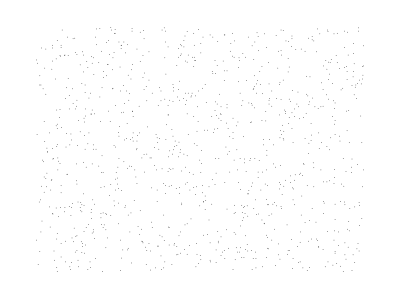

```mathematica
pts={RandomInteger[600],RandomInteger[450]}&/@Range@1000;
Framed@Graphics[{PointSize[.001],Point@pts}]
```

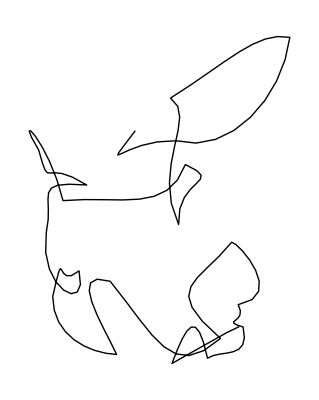

```mathematica
Graphics[{Thin,BezierCurve@Accumulate@RandomReal[{-1,1},{60,2}]}]
```

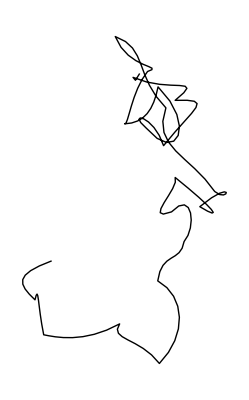

```mathematica
Graphics[{Thin,BezierCurve@Accumulate@RandomReal[{-1,1},{60,2}]}]
```

```mathematica
pln=1000;
series=RandomInteger[{1,6},{pln,3}];
Short@%
```

{{2,1,3},{3,1,5},{3,4,5},{2,6,4},{1,5,6},«990»,{2,3,5},{3,3,3},{3,4,6},{1,1,5},{6,1,5}}

{6,9,12,12,12,10,12,8,13,12,10,13,8,9,9,9,«968»,10,8,9,10,8,10,7,7,12,14,17,10,9,13,7,12}

{3→2,4→16,5→29,6→49,7→61,8→108,9→134,10→118,11→103,12→113,13→114,14→72,15→48,16→11,17→18,18→4}

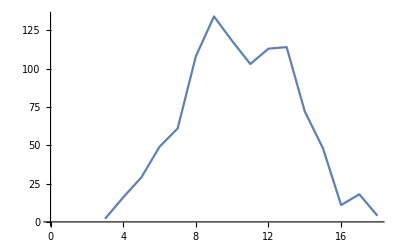

```mathematica
tot=Total/@series;Short@tot
counts=SortBy[Normal@Counts@tot,First]
ListLinePlot[List@@@counts]
```

```mathematica
mean=Mean@tot
sDev=StandardDeviation@tot
```

10439/1000

(√(8572279/1110))/30

```mathematica
nd=PDF[NormalDistribution[mean,sDev],x]
```

30 ⅇ^(-(499500 (-10439/1000+x)^2)/8572279) √(555/(8572279 π))

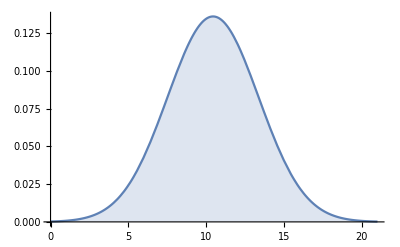

```mathematica
Plot[nd//Evaluate,{x,0,21},Filling->Axis]
```

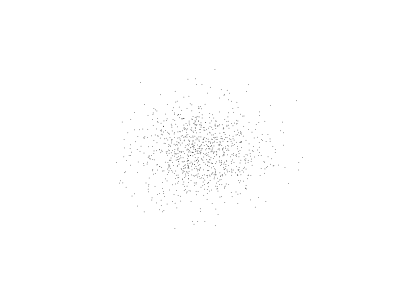

```mathematica
pts=RandomVariate[NormalDistribution[0,.1],2] {600,450}&/@Range@1000;
Framed@Graphics[{PointSize[.001],Point@pts},PlotRange->{{-300,300},{-225,225}}]
```

### Parametric and Individuals

```mathematica
BR2[len_,rot_,ite_]:=Module[{},If[ite==0,Return[]];
{Line[{{0,0},{0,len}}],Translate[{Rotate[{BR2[LinkLength@len,rot,ite-1]},LinkRotation@rot,{0,0}],Rotate[{BR2[LinkLength@len,rot,ite-1]},-LinkRotation@rot,{0,0}]},{0,len}]}]
δ1=NormalDistribution[2,.1];
δ2=NormalDistribution[6,1];
LinkLength[len_]:=len/RandomVariate@δ1
LinkRotation[rot_]:=π/RandomVariate@δ2
```

```mathematica
tree:=Graphics[BR2[1,π/6,6],PlotRange->{{-.9,.9},{0,2.2}},ImageSize->64]
Grid@Partition[Table[tree,{i,1,16}],4]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

### The Markov Chain and Machine Learning

```mathematica
series={1,2,1,1,2,1,2,3,2,1,1,2,3,1,2};
```

```mathematica
states=DeleteDuplicates@series
```

{1,2,3}

```mathematica
transitions=Partition[series,2,1]
```

{{1,2},{2,1},{1,1},{1,2},{2,1},{1,2},{2,3},{3,2},{2,1},{1,1},{1,2},{2,3},{3,1},{1,2}}

```mathematica
follow=#[[2]]&/@Extract[transitions,Position[transitions,{#,_}]]&/@states
```

{{2,1,2,2,1,2,2},{1,1,3,1,3},{2,1}}

```mathematica
C1[fol_,states_]:=(Length@Position[fol,#]&/@states)/Length@fol
```

```mathematica
pm=C1[#,states]&/@follow
```

{{2/7,5/7,0},{3/5,0,2/5},{1/2,1/2,0}}

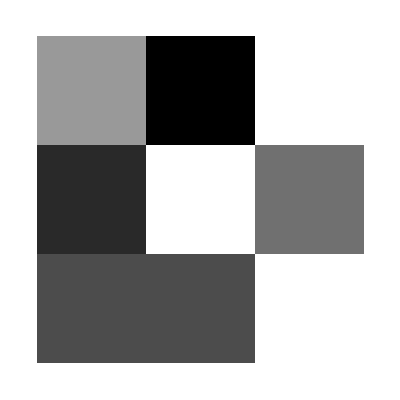

```mathematica
ArrayPlot@pm
```

```mathematica
P=DiscreteMarkovProcess[1,pm];
```

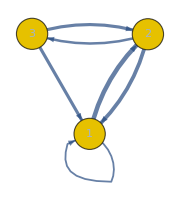

```mathematica
el=Flatten@Table[DirectedEdge[i,j]->Thickness[pm[[i,j]]/40],{i,Length@pm},{j,Length@pm}];
eld=Delete[el,Position[el,_->Thickness[0]]];
Graph[DiscreteMarkovProcess[1,pm],EdgeStyle->eld,ImageSize->Small]
```

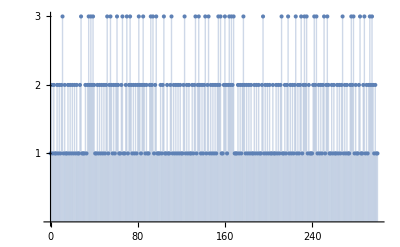

```mathematica
data=RandomFunction[P,{0,300}];
ListPlot[data,Filling->Axis,Ticks->{Automatic,{1,2,3}}]
```